# Code for Additional Figures

This file contains the code for all other figures included in the paper (Figs 1, 2, and A.1-4).

## Figure 1

Code for creating the 9 subfigures of Fig 1. Note that, as this code is stochastic, you cannot reproduce exactly the same figures due to differences between runs. Subfigures were compiled in Adobe Illustrator 2024.

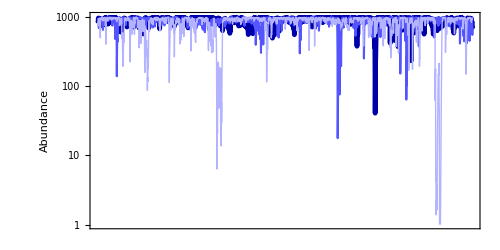

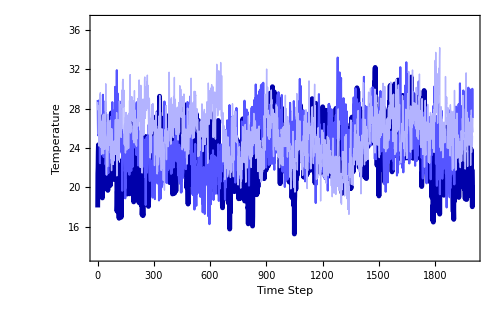

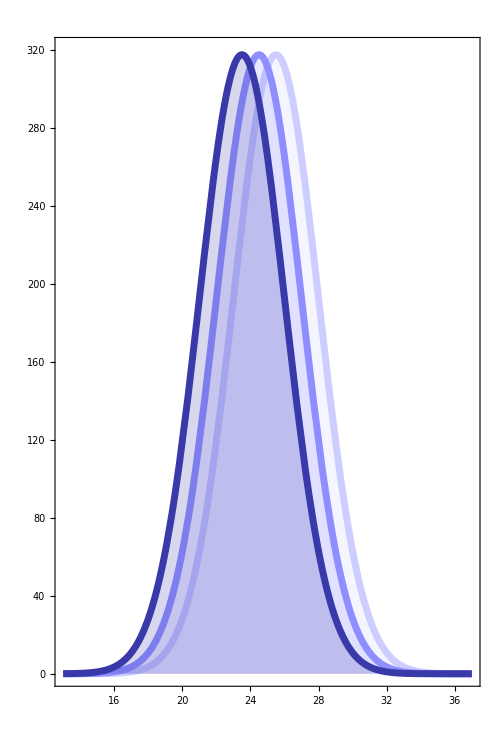

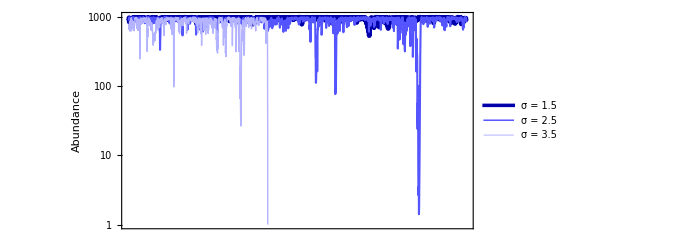

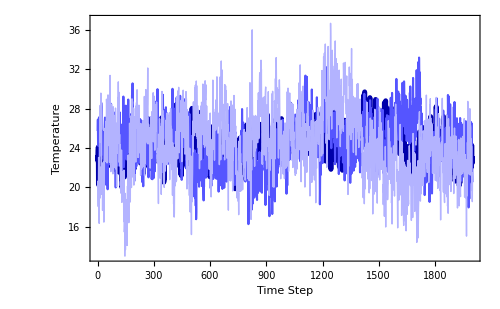

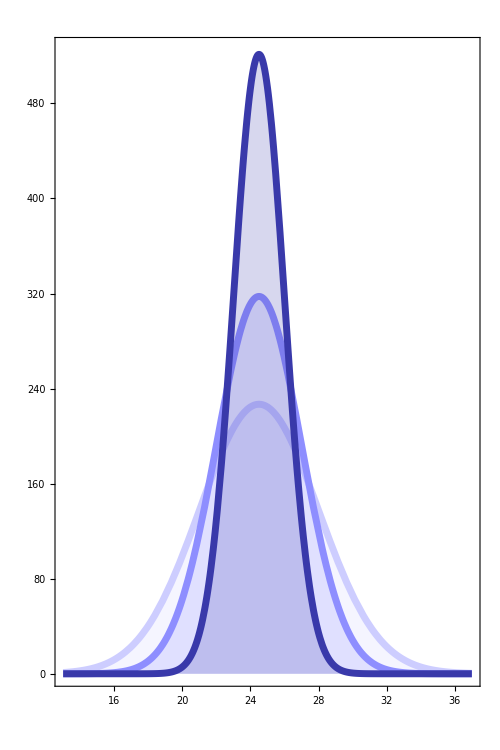

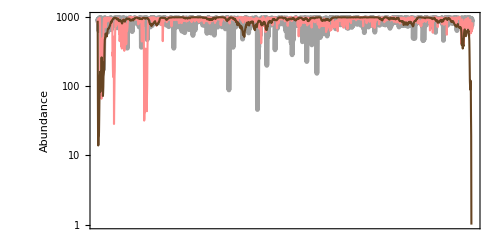

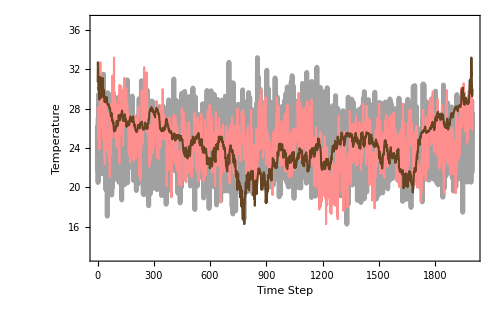

```mathematica
(*background functions*)
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,1,1/Nobs];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/(f[[i]]^(γ/2)),phase[[i]]],{i,1,(Nobs-1)}]],FourierParameters->{-1,1}];
Standardize[Re[vec]]*σ+μ];

Mimic1[x_,z_]:=Module[{y},
y=x;
Do [y[[Ordering[z,i][[i]]]]=x[[i]],{i,1,Length[x]}];
y];

gain[T_]:=Exp[-((T-TI)^2)/β];
loss[T_]:=ma Exp[mb T]+mc;
r[T_]:=(gain[T]-loss[T])/.755; 

TI=29; β=180; 
ma=0.000005;mb=0.4;mc=0.05;

nt[t_,ntlast_]:=(r[Z[[t]]]Exp[r[Z[[t]]] ])/((r[Z[[t]]]/ntlast-α)+α Exp[r[Z[[t]]]]);

(*Subplot a: varying the mean temperature*)
α=.001;
tmax=2000; (*2000*)
maxsims=1; (*1000*)
γvals=Range[1,1,1];  (*Autocorrelation: Range[0,2,.1] -> 21*)
μTvals=Range[23.5,25.5,1]; (*Mean temp: Range[23,26,1] -> 4*)
σTvals=Range[2.5,2.5,1]; (*St dev of temp: Range[3,3,1] -> 1*)

W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
p1=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p1[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

temps1=ConstantArray[0,Length[μTvals]];

SetSharedVariable[p1,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps1[[j]]=Z;

Do[p1[[i,j,m,l,k]]=nt[k,p1[[i,j,m,l,k-1]]];
If[p1[[i,j,m,l,k]]<((1/α)*10^-6),extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*subplot b: varying the st dev of temperature*)
γvals=Range[1,1,1];  (*Autocorrelation: Range[0,2,.1] -> 21*)
μTvals=Range[24.5,24.5,1]; (*Mean temp: Range[23,26,1] -> 4*)
σTvals=Range[1.5,3.5,1]; (*St dev of temp: Range[3,3,1] -> 1*)

W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
p2=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p2[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

temps2=ConstantArray[0,Length[σTvals]];

SetSharedVariable[p2,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps2[[m]]=Z;

Do[p2[[i,j,m,l,k]]=nt[k,p2[[i,j,m,l,k-1]]];
If[p2[[i,j,m,l,k]]<((1/α)*10^-6),extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*subplot c: varying the autocorrelation of temperature*)
γvals=Range[0,2,1];  (*Autocorrelation: Range[0,2,.1] -> 21*)
μTvals=Range[24.5,24.5,1]; (*Mean temp: Range[23,26,1] -> 4*)
σTvals=Range[2.5,2.5,1]; (*St dev of temp: Range[3,3,1] -> 1*)

W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

ninit=ConstantArray[0,{Length[μTvals],Length[σTvals]}];
Do[ninit[[i,k]]=(Mean[Table[r[W[[i,k,j]]],{j,1,tmax}]])/α,{k,1,Length[σTvals]},{i,1,Length[μTvals]}]

extTime=ConstantArray[tmax,{Length[γvals],Length[μTvals],Length[σTvals],maxsims}];
p3=ConstantArray[0,{Length[γvals],Length[μTvals],Length[σTvals],maxsims,tmax}];
Do[p3[[i,j,m,l,1]]=ninit[[j,m]],{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

temps3=ConstantArray[0,Length[γvals]];

SetSharedVariable[p3,extTime];
Do[γ=γvals[[i]];
μT=μTvals[[j]];
σT=σTvals[[m]];

X=SpecSynFourier[γ,tmax];
Z=Mimic1[W[[j,m]],X];
envt=Interpolation[Z,InterpolationOrder->0];

temps3[[i]]=Z;

Do[p3[[i,j,m,l,k]]=nt[k,p3[[i,j,m,l,k-1]]];
If[p3[[i,j,m,l,k]]<((1/α)*10^-6),extTime[[i,j,m,l]]=k;
Break[]];,{k,2,tmax}],

{l,1,maxsims},{m,1,Length[σTvals]},{j,1,Length[μTvals]},{i,1,Length[γvals]}]

(*plotting code*)
plotstyle={{Thickness[0.007],Darker[Blue]},{Thickness[0.003],Lighter[Blue]},{Thickness[0.002],Lighter[Lighter[Lighter[Blue]]]}};
plotstyle2={{Thickness[0.007],Lighter[Darker[Lighter[Gray]]]},{Thickness[0.003],Lighter[Lighter[Red]]},{Thickness[0.003],Darker[Brown]}}; 
size=24;
size2=38;

μfticks=Table[{i,Rotate[i,90 Degree]},{i,0,320,100}];
data1={p1[[1,1,1,1]],p1[[1,2,1,1]],p1[[1,3,1,1]]};
μabundances=ListLinePlot[data1,ScalingFunctions->{"Linear","Log"},PlotStyle->plotstyle,PlotRange->{{0,2000},{1,1020}},FrameTicks->{{Automatic, None},{None,None}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{(*"Time Step"*)None,"Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.5]
μtemperatures=ListLinePlot[{temps1[[1]],temps1[[2]],temps1[[3]]},PlotStyle->plotstyle,PlotRange->{{0,2000},{13,37}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{"Time Step","Temperature"},LabelStyle->Directive[Black],ImageSize->500]
fticks=Table[{i,Rotate[i,90 Degree]},{i,0,320,100}];
μtempshist=Rotate[Show[Plot[1990*PDF[NormalDistribution[25.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Lighter[Lighter[Lighter[Lighter[Blue]]]]},Filling->Axis,PlotRange->{{13,37},{0,320}}, Frame->{True,False,False,True},FrameStyle->14,FrameLabel->{None(*"Temperature"*),None,None,"Frequency"},FrameTicks->{{None,fticks},{None,None}},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->1.5],Plot[1990*PDF[NormalDistribution[24.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Lighter[Lighter[Blue]]},Filling->Axis],Plot[1990*PDF[NormalDistribution[23.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Darker[Lighter[Blue]]},Filling->Axis]],270Degree]

σfticks=Table[{i,Rotate[i,90 Degree]},{i,0,520,100}];
data2={p2[[1,1,1,1]],p2[[1,1,2,1]],p2[[1,1,3,1]]};
σabundances=ListLinePlot[data2,ScalingFunctions->{"Linear","Log"},PlotStyle->plotstyle,PlotLegends->Placed[{"σ = 1.5","σ = 2.5","σ = 3.5"},{0.6,0.2}],PlotRange->{{0,2000},{1,1020}},FrameTicks->{{Automatic, None},{None,None}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{(*"Time Step"*)None,"Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.5]
σtemperatures=ListLinePlot[{temps2[[1]],temps2[[2]],temps2[[3]]},PlotStyle->plotstyle,PlotRange->{{0,2000},{13,37}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{"Time Step","Temperature"},LabelStyle->Directive[Black],ImageSize->500]
fticks=Table[{i,Rotate[i,90 Degree]},{i,0,520,100}];
σtempshist=Rotate[Show[Plot[1990*PDF[NormalDistribution[24.5,3.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Lighter[Lighter[Lighter[Lighter[Blue]]]]},Filling->Axis,PlotRange->{{13,37},{0,525}}, Frame->{True,False,False,True},FrameStyle->14,FrameLabel->{None(*"Temperature"*),None,None,"Frequency"},FrameTicks->{{None,fticks},{None,None}},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->1.5],Plot[1990*PDF[NormalDistribution[24.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Lighter[Lighter[Blue]]},Filling->Axis],Plot[1960*PDF[NormalDistribution[24.5,1.5],x],{x,13,37},PlotStyle->{Thickness[0.01],Darker[Lighter[Blue]]},Filling->Axis]],270 Degree]

γfticks=Table[{i,Rotate[i,90 Degree]},{i,0,320,100}];
data3={p3[[1,1,1,1]],p3[[2,1,1,1]],p3[[3,1,1,1]]};
γabundances=ListLinePlot[data3,ScalingFunctions->{"Linear","Log"},PlotStyle->plotstyle2,PlotRange->{{0,2000},{1,1020}},FrameTicks->{{Automatic, None},{None,None}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{(*"Time Step"*)None,"Abundance"},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->.5]
γtemperatures=ListLinePlot[{temps3[[1]],temps3[[2]],temps3[[3]]},PlotStyle->plotstyle2,PlotRange->{{0,2000},{13,37}},Frame->{True,True,False,False},FrameStyle->size,FrameLabel->{"Time Step","Temperature"},LabelStyle->Directive[Black],ImageSize->500]
fticks=Table[{i,Rotate[i,90 Degree]},{i,0,320,100}];
tticks=Table[{i,Rotate[i,90Degree]},{i,15,35,5}];
γtempshist=Rotate[Show[Plot[1990*PDF[NormalDistribution[24.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.018],Lighter[Gray]},Filling->Axis,PlotRange->{{13,37},{0,320}}, Frame->{True,False,False,True},FrameStyle->14,FrameLabel->{(*Rotate["Temperature",90 Degree],*)None,None,None,"Frequency"},FrameTicks->{{None,fticks},{None,None}},LabelStyle->Directive[Black],ImageSize->500,AspectRatio->1.5],Plot[1990*PDF[NormalDistribution[24.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.013],Lighter[Lighter[Red]]},Filling->Axis],Plot[1990*PDF[NormalDistribution[24.5,2.5],x],{x,13,37},PlotStyle->{Thickness[0.005],Darker[Brown]},Filling->Axis]],270Degree]

saveto="/EXPORTLOCATION/";
Export[saveto<>"muabundance.pdf",μabundances,ImageResolution->1000];
Export[saveto<>"mutemperatures.pdf",μtemperatures,ImageResolution->1000];
Export[saveto<>"mutempshist.pdf",μtempshist,ImageResolution->1000];

Export[saveto<>"sigabundance.pdf",σabundances,ImageResolution->1000];
Export[saveto<>"sigtemperatures.pdf",σtemperatures,ImageResolution->1000];
Export[saveto<>"sigtempshist.pdf",σtempshist,ImageResolution->1000];

Export[saveto<>"gammaabundance.pdf",γabundances,ImageResolution->1000];
Export[saveto<>"gammatemperatures.pdf",γtemperatures,ImageResolution->1000];
Export[saveto<>"gammatempshist.pdf",γtempshist,ImageResolution->1000];
```

## Figure 2

This code creates a figure of the generic TPCs used in the initial models.

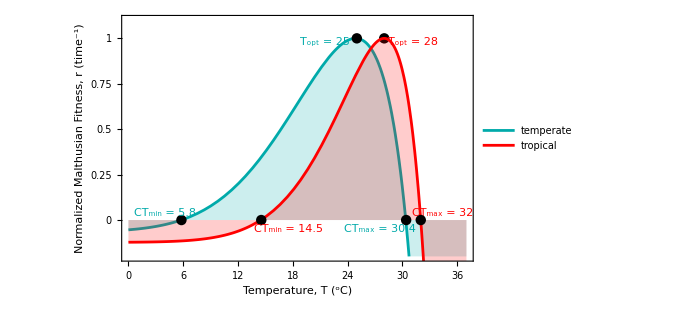

```mathematica
gain[T_,TI_,β_]:=Exp[-((T-TI)^2)/β];
loss[T_,ma_,mb_,mc_]:=ma Exp[mb T]+mc;
r[T_,TI_,β_,ma_,mb_,mc_]:=gain[T,TI,β]-loss[T,ma,mb,mc];

TI=29; β=180; 
ma=0.000005;mb=0.4;mc=0.05;

TI1=35;β1=170;

TPCs=Show[Plot[r[T,TI,β,ma,mb,mc]/.755,{T,0,37},Filling->Axis,PlotStyle->Darker[Cyan],PlotLegends->Placed[{"temperate"},{0.2,0.8}],PlotRange->{{0,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Malthusian Fitness, r (time^-1)"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500,PlotRange->{-0.2,1.1}],
Plot[(r[T-2,TI1,β1,ma,mb,mc])/.4067,{T,0,37},Filling->Axis,PlotStyle->Red,PlotLegends->Placed[{"tropical"},{0.182,0.7}]],Epilog->{{Text[Style["T_opt = 25",Darker[Cyan]],{21.5,.98}]},{Text[Style["CT_min = 5.8",Darker[Cyan]],{4,.04}]},{Text[Style["CT_max = 30.4",Darker[Cyan]],{27.5,-.05}]},{Text[Style["T_opt = 28",Red],{31.2,.98}]},
{Text[Style["CT_min = 14.5",Red],{17.5,-.05}]},{Text[Style["CT_max = 32",Red],{34.4,.04}]},
{Black,PointSize[0.015],Point[{5.8,0}]},
{Black,PointSize[0.015],Point[{14.54,0}]},{Black,PointSize[0.015],Point[{25,1}]},
{Black,PointSize[0.015],Point[{28,1}]},
{Black,PointSize[0.015],Point[{30.4,0}]},{Black,PointSize[0.015],Point[{32,0}]}}]

Export[saveto<>"Fig2.pdf",TPCs,ImageResolution->1000]
```

## Figure A.1

This recreates the Gaussian-quadratic TPC of the organisms most similar to those used in initial models.

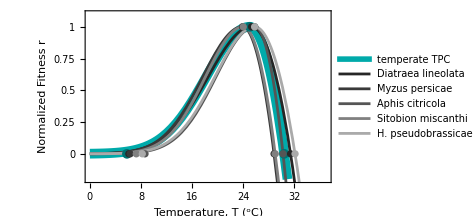
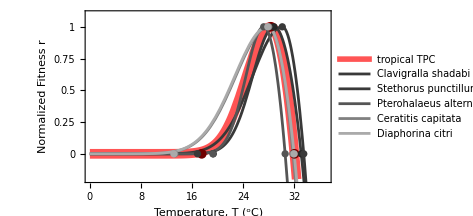

/Users/alisonrobey/Documents/PhD Year 3 (2023-2024)/Ch1/Code/TPCsComparison_Deutschfit.eps

```mathematica
rD[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 

(*temporate TPCs*)
CTmax=31.4;Topt=25.3;σp=4.8;
CTmax2=28.82;Topt2=23.88;σp2=4.395;
CTmax3=30.225;Topt3=25.8;σp3=4.29375;
CTmax4=29;Topt4=24;σp4=4.185;
CTmax5=32.1;Topt5=25.78;σp5=4.395;

(*tropical TPCs*)
TCTmax=33.0677;TTopt=28.8;Tσp=2.375;
TCTmax2=33.46;TTopt2=30.1;Tσp2=3.315;
TCTmax3=30.55;TTopt3=27.2;Tσp3=1.9875;
TCTmax4=31.78;TTopt4=27.98;Tσp4=3.675;
TCTmax5=31.96;TTopt5=27.84;Tσp5=3.675;

DeutschTPCs=Show[Plot[rD[T,25,4.8,30.4],{T,0,37},PlotStyle->{Darker[Cyan],Thickness[0.02]},PlotLegends->Placed[{"temperate TPC"},{0.22,0.8}],PlotRange->{{0,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500,PlotRange->{-0.2,1.1}],
Plot[rD[T,Topt,σp,CTmax],{T,0,37},PlotLegends->Placed[{"Diatraea lineolata"},{0.22,0.75}],PlotStyle->Darker[Darker[Darker[Gray]]]],
Plot[rD[T,Topt2,σp2,CTmax2],{T,0,37},PlotLegends->Placed[{"Myzus persicae"},{0.22,0.7}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,Topt3,σp3,CTmax3],{T,0,37},PlotLegends->Placed[{"Aphis citricola"},{0.22,0.65}],PlotStyle->Darker[Gray]],
Plot[rD[T,Topt4,σp4,CTmax4],{T,0,37},PlotLegends->Placed[{"Sitobion miscanthi"},{0.22,0.6}],PlotStyle->Gray],
Plot[rD[T,Topt5,σp5,CTmax5],{T,0,37},PlotLegends->Placed[{"H. pseudobrassicae"},{0.22,0.55}],PlotStyle->Lighter[Gray]],

Epilog->{{Darker[Darker[Cyan]],PointSize[0.02],Point[{30.4,0}]},
{Darker[Darker[Cyan]],PointSize[0.02],Point[{25,1}]},{Darker[Darker[Cyan]],PointSize[0.02],Point[{5.8,0}]},

{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{CTmax,0}]},
{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{Topt,1}]},{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{6.1,0}]},

{Darker[Darker[Gray]],PointSize[0.015],Point[{CTmax2,0}]},
{Darker[Darker[Gray]],PointSize[0.015],Point[{Topt2,1}]},{Darker[Darker[Gray]],PointSize[0.015],Point[{6.3,0}]},

{Darker[Gray],PointSize[0.015],Point[{CTmax3,0}]},
{Darker[Gray],PointSize[0.015],Point[{Topt3,1}]},{Darker[Gray],PointSize[0.015],Point[{8.625,0}]},

{Gray,PointSize[0.015],Point[{CTmax4,0}]},
{Gray,PointSize[0.015],Point[{Topt4,1}]},{Gray,PointSize[0.015],Point[{7.26,0}]},

{Lighter[Gray],PointSize[0.015],Point[{CTmax5,0}]},
{Lighter[Gray],PointSize[0.015],Point[{Topt5,1}]},{Lighter[Gray],PointSize[0.015],Point[{8.2,0}]}},
ImageSize->350];

DeutschTPCsTrop=Show[Plot[rD[T,28.3,2.7,32],{T,0,37},PlotStyle->{Lighter[Red],Thickness[0.02]},PlotLegends->Placed[{"tropical TPC"},{0.3,0.8}],PlotRange->{{0,37},{-.2,1.1}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},ImageSize->500,PlotRange->{-0.2,1.1}],
Plot[rD[T,TTopt,Tσp,TCTmax],{T,0,37},PlotLegends->Placed[{"Clavigralla shadabi"},{0.3,0.75}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,TTopt2,Tσp2,TCTmax2],{T,0,37},PlotLegends->Placed[{"Stethorus punctillum"},{0.3,0.7}],PlotStyle->Darker[Darker[Gray]]],
Plot[rD[T,TTopt3,Tσp3,TCTmax3],{T,0,37},PlotLegends->Placed[{"Pterohalaeus alternatus"},{0.3,0.65}],PlotStyle->Darker[Gray]],
Plot[rD[T,TTopt4,Tσp4,TCTmax4],{T,0,37},PlotLegends->Placed[{"Ceratitis capitata"},{0.3,0.6}],PlotStyle->Gray],
Plot[rD[T,TTopt5,Tσp5,TCTmax5],{T,0,37},PlotLegends->Placed[{"Diaphorina citri"},{0.3,0.55}],PlotStyle->Lighter[Gray]],

Epilog->{{Darker[Darker[Red]],PointSize[0.02],Point[{32,0}]},
{Darker[Darker[Red]],PointSize[0.02],Point[{28.3,1}]},{Darker[Darker[Red]],PointSize[0.02],Point[{17.5,0}]},

{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{TCTmax,0}]},
{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{TTopt,1}]},{Darker[Darker[Darker[Gray]]],PointSize[0.015],Point[{19.3,0}]},

{Darker[Darker[Gray]],PointSize[0.015],Point[{TCTmax2,0}]},
{Darker[Darker[Gray]],PointSize[0.015],Point[{TTopt2,1}]},{Darker[Darker[Gray]],PointSize[0.015],Point[{16.84,0}]},

{Darker[Gray],PointSize[0.015],Point[{TCTmax3,0}]},
{Darker[Gray],PointSize[0.015],Point[{TTopt3,1}]},{Darker[Gray],PointSize[0.015],Point[{19.25,0}]},

{Gray,PointSize[0.015],Point[{TCTmax4,0}]},
{Gray,PointSize[0.015],Point[{TTopt4,1}]},{Gray,PointSize[0.015],Point[{13.28,0}]},

{Lighter[Gray],PointSize[0.015],Point[{TCTmax5,0}]},
{Lighter[Gray],PointSize[0.015],Point[{TTopt5,1}]},{Lighter[Gray],PointSize[0.015],Point[{13.14,0}]}},
ImageSize->350];

stackedTPCs=Row[{DeutschTPCs,DeutschTPCsTrop}]

Export[saveto<>"TPCsComparison_Deutschfit.pdf",stackedTPCs,ImageResolution->1000]
```

## Figures A.2 & A.3

This code tests the impact of the timestep size, δt, on population dynamics. Models are stochastic, so will not output exactly the same graphs on every run.

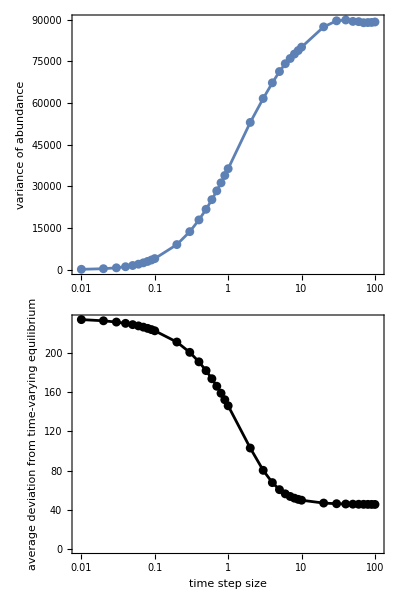

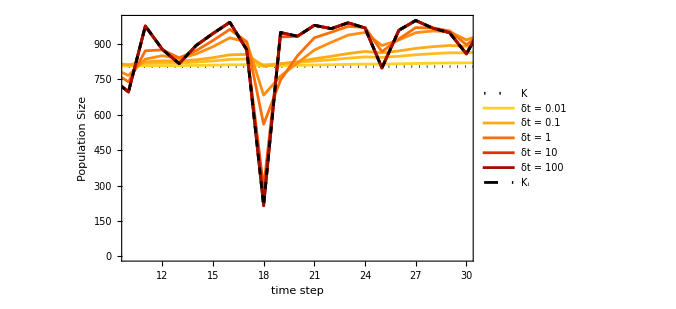

```mathematica
(*background functions - same as other versions with δt added in and an edit to the indexing in Z to allow for multiple runs*)
r[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 

nt[t_,ntlast_,δt_,i_]:=(r[Z[[i,t]],Topt,σp,CTmax]*Exp[r[Z[[i,t]],Topt,σp,CTmax]*δt ])/((r[Z[[i,t]],Topt,σp,CTmax]/ntlast-α)+α Exp[r[Z[[i,t]],Topt,σp,CTmax]*δt]);

(*unchanging parameters for TPC and temps*)
Topt=25;σp=5;CTmax=30; (*TPC params*)
α=.001;
μT=25; σT=3; (*temp params-values for some extinction risk*)

tmax=100; (*number of time steps*)
nmax=500; (*number of replicates*)

(*initializing*)
δts=Join[Range[0.01,0.09,0.01],Range[0.1,0.9,0.1],Range[1,10],Range[20,100,10]];

means=vars=stdevs=ConstantArray[0,{nmax,Length[δts]}];
cvs=equidists=ConstantArray[0,Length[δts]];
extTime=ConstantArray[tmax,{nmax,Length[δts]}];

(*set up thermal regimes*)
Z=ConstantArray[0,{nmax,tmax}];
Do[Z[[i,k]]=RandomVariate[NormalDistribution[μT,σT]],
{k,1,tmax},{i,1,nmax}];

μr=ConstantArray[0,nmax];
Do[μr[[i]]=Mean[Table[r[Z[[i,k]],Topt,σp,CTmax],{k,1,tmax}]],{i,1,nmax}];

ninit=ConstantArray[0,nmax];
Do[ninit[[i]]=μr[[i]]/α,{i,1,nmax}];

Ks=ConstantArray[0,{nmax,tmax}];
Do[Ks[[i,k]]=r[Z[[i,k]],Topt,σp,CTmax]/α,{k,1,tmax},{i,1,nmax}];

p=ConstantArray[0,{nmax,Length[δts],tmax}];
Do[p[[i,All,1]]=ninit[[i]],{i,1,nmax}];

(*simulations*)
Do[p[[i,j,k]]=nt[k,p[[i,j,k-1]],δts[[j]],i];
If[p[[i,j,k]]<((1/α)*10^-6),extTime[[i,j]]=k(*;Break[]*)],
{k,2,tmax},{j,1,Length[δts]},{i,1,nmax}]

(*calculate stats*)
Do[If[extTime[[i,j]]==tmax,

means[[i,j]]=Mean[p[[i,j]]];
vars[[i,j]]=Variance[p[[i,j]]];
stdevs[[i,j]]=StandardDeviation[p[[i,j]]],

means[[i,j]]=Mean[Take[p[[i,j]],extTime[[i,j]]]];
vars[[i,j]]=Variance[Take[p[[i,j]],extTime[[i,j]]]];
stdevs[[i,j]]=StandardDeviation[Take[p[[i,j]],extTime[[i,j]]]];

],{j,1,Length[δts]},{i,1,nmax}]

allmeans=Mean[means];allvars=Mean[vars];allstdevs=Mean[stdevs];
meanplot=Transpose[{δts,allmeans}];varplot=Transpose[{δts,allvars}];stdevplot=Transpose[{δts,allstdevs}];

ListLogLinearPlot[meanplot,PlotLabel->"Means"];
ListLogLinearPlot[varplot,PlotLabel->"Vars"];
ListLogLinearPlot[stdevplot,PlotLabel->"Stdevs"];

Do[cvs[[j]]=allstdevs[[j]]/allmeans[[j]],
{j,1,Length[δts]}];
cvplot=Transpose[{δts,cvs}];
ListLogLinearPlot[cvplot,PlotLabel->"CVs"];

dist=ConstantArray[0,{nmax,Length[δts],tmax}];
Do[dist[[i,j,k]]=Abs[Ks[[i,k]]-p[[i,j,k]]],{k,1,tmax},{j,1, Length[δts]},{i,1,nmax}];
meandist=ConstantArray[0,{nmax,Length[δts]}];
Do[meandist[[i,j]]=Mean[dist[[i,j]]],{j,1, Length[δts]},{i,1,nmax}];
meandists=Mean[meandist];
meandistplot=Transpose[{δts,meandists}];
ListLogLinearPlot[meandistplot,PlotLabel->"MeanDists"];

timestepplot=Column[{
Show[ListLogLinearPlot[varplot,Joined->True,PlotRange->{{0.009,110},Automatic},GridLines->{δts,None},
Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{None,"variance of abundance"},AspectRatio->.4,ImageSize->500],ListLogLinearPlot[varplot]],
Show[ListLogLinearPlot[meandistplot,PlotStyle->Black,Joined->True,PlotRange->{{0.009,110},Automatic},GridLines->{δts,None},
Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"time step size","average deviation from \n time-varying equilibrium"},AspectRatio->.4,ImageSize->500],ListLogLinearPlot[meandistplot,PlotStyle->Black]]},Spacings->{0,0}]

colorFunc=ColorData["SolarColors"];
run=15;
total=9;
line=ConstantArray[ninit[[run]],tmax];
timestepseriesplot=Show[
ListLinePlot[line,PlotRange->{{10,30},{0,1000}},PlotStyle->{Black,Dotted},PlotLegends->{"K"},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"time step","Population Size"}],
ListLinePlot[p[[run,1]],PlotStyle->colorFunc[9/total],PlotLegends->{"δt = 0.01"}],
ListLinePlot[p[[run,5]],PlotStyle->colorFunc[8/total](*,PlotLegends->{"δt = 0.05"}*)],
ListLinePlot[p[[run,10]],PlotStyle->colorFunc[7/total],PlotLegends->{"δt = 0.1"}],
ListLinePlot[p[[run,14]],PlotStyle->colorFunc[6/total](*,PlotLegends->{"δt = 0.5"}*)],
ListLinePlot[p[[run,19]],PlotStyle->colorFunc[5/total],PlotLegends->{"δt = 1"}],
ListLinePlot[p[[run,23]],PlotStyle->colorFunc[4/total](*,PlotLegends->{"δt = 5"}*)],
ListLinePlot[p[[run,28]],PlotStyle->colorFunc[3/total],PlotLegends->{"δt = 10"}],
ListLinePlot[p[[run,32]],PlotStyle->colorFunc[2/total](*,PlotLegends->{"δt = 50"}*)],
ListLinePlot[p[[run,37]],PlotStyle->colorFunc[1/total],PlotLegends->{"δt = 100"}],
ListLinePlot[Ks[[run]],PlotStyle->{Black,Dashed},PlotLegends->{Subscript["K","i"]}],
ImageSize->500]

Export[saveto<>"timestepplot.pdf",timestepseriesplot,ImageResolution->1000]
Export[saveto<>"timestepseriesplot.pdf",timestepplot,ImageResolution->1000]
```